```mathematica
(*Here we consider a 1D Bloch periodic Schrodinger equation. We calculate the dipole moment in a unit cell and then compute its change numerically. We show that the change in polarization is not unique.
NB:-
1. Run this on DELL Desktop, not on laptop. 
2. Make sure to run the calculation a few times, sometimes i get erroneous results. Save, shutdown, restart and them do the computation.
3. Don't do anything else on this computer while performing this computation, it can give erroneous results.
4. Some details of the computation are available in the OneNote File "Polarization->Error in resta-> 1DSchrodinger eqn"*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
L:=5(*length of the unit cell [0,L]*)
```

```mathematica
Ntot:=32(*no. of sampling points for 1D BZ*)
```

```mathematica
ntot:=2(*no of bands*)
```

```mathematica
a:=-L/2(*starting point of unit cell*)
```

```mathematica
A[t_]:=t^2(*Sin[t]*)(*The parameter modulating the change in Potential*)
```

```mathematica
V[x_,t_]:=3+Cos[2*Pi*1*x/L-t](*{3+A[t]*Cos[2*Pi*10*x/L],}*)
```

```mathematica
ρ[x_]:=0
```

```mathematica
ρ1[x_]:=0
```

```mathematica
λ=1.00000;
```

```mathematica
Δλ=0.00001;
```

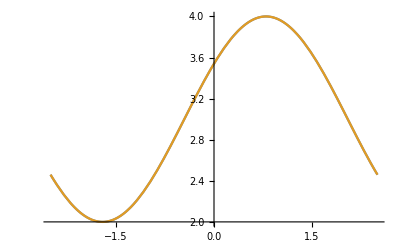

```mathematica
Plot[{V[x,λ],V[x,λ+Δλ]},{x,a,a+L}]
```

```mathematica
(*Looping over each point in the BZ*)
```

```mathematica
(*We assume that the first 3 bands are filled*)
For[n=1,n<=ntot,n++,
For[i=1,i<=Ntot,i++,
k:=((2*i-Ntot-1)/(2*Ntot))*2*Pi/L;
vals=NDEigenvalues[{-Laplacian[u[x],{x}]-2*I*k*D[u[x],x]+k^2*u[x]+V[x,λ]*u[x],u[a]==u[a+L]},u[x],{x,a,a+L},ntot];
(*ufun=NDSolve[{-Laplacian[u[x],{x}]-2*I*k*D[u[x],x]+k^2*u[x]+V[x,λ]*u[x]==vals[[n]]*u[x],u[a]==u[a+L],u[a]==1.2},u[x],{x,a,a+L}];*)ufun=NDSolve[{-Laplacian[u[x],{x}]-2*I*k*D[u[x],x]+k^2*u[x]+V[x,λ]*u[x]==vals[[n]]*u[x],u[a]==u[a+L],u[a+0.0*L]==0.2},u[x],{x,a,a+L}];
v[x_]:=Evaluate[u[x]/.ufun]/Sqrt[NIntegrate[Abs[Evaluate[u[x]/.ufun]]^2,{x,a,a+L}]];(*myperiodic[Evaluate[u[x]/.ufun]/NIntegrate[Abs[Evaluate[u[x]/.ufun]]^2,{x,a,a+L}], {x, a, a+L}];*)
ρ[x]=ρ[x]+Abs[v[x]]^2;
]
]
```

```mathematica
ρ[x]=ρ[x]/(Ntot*(2*Pi)/L);
```

```mathematica
(*q[x]=-D[ρ[x],x];*)
```

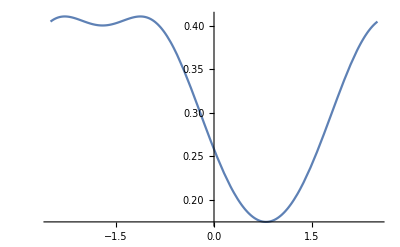

```mathematica
Plot[{ρ[x]}, {x, a, a + L}]
```

```mathematica
NIntegrate[ρ[x]*(x-a),{x,a,a+L}]
```

{3.62851}

```mathematica
λ1=λ+Δλ
```

1.00001

```mathematica
Clear[vals,ufun,v]
```

```mathematica
(*We assume that the first 3 bands are filled*)
For[n=1,n<=ntot,n++,
For[i=1,i<=Ntot,i++,
k:=((2*i-Ntot-1)/(2*Ntot))*2*Pi/L;
vals=NDEigenvalues[{-Laplacian[u[x],{x}]-2*I*k*D[u[x],x]+k^2*u[x]+V[x,λ1]*u[x],u[a]==u[a+L]},u[x],{x,a,a+L},ntot];
(*ufun=NDSolve[{-Laplacian[u[x],{x}]-2*I*k*D[u[x],x]+k^2*u[x]+V[x,λ]*u[x]==vals[[n]]*u[x],u[a]==u[a+L],u[a]==1.2},u[x],{x,a,a+L}];*)ufun=NDSolve[{-Laplacian[u[x],{x}]-2*I*k*D[u[x],x]+k^2*u[x]+V[x,λ1]*u[x]==vals[[n]]*u[x],u[a]==u[a+L],u[a+0.0*L]==0.2},u[x],{x,a,a+L}];
v[x_]:=Evaluate[u[x]/.ufun]/Sqrt[NIntegrate[Abs[Evaluate[u[x]/.ufun]]^2,{x,a,a+L}]];(*myperiodic[Evaluate[u[x]/.ufun]/NIntegrate[Abs[Evaluate[u[x]/.ufun]]^2,{x,a,a+L}], {x, a, a+L}];*)
ρ1[x]=ρ1[x]+Abs[v[x]]^2;
]
]
```

```mathematica
ρ1[x]=ρ1[x]/(Ntot*(2*Pi)/L);
```

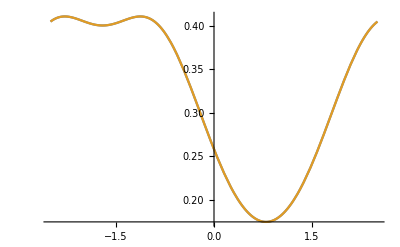

```mathematica
Plot[{ρ[x],ρ1[x]}, {x, a, a+L}]
```

```mathematica
NIntegrate[ρ1[x]*(x-a),{x,a,a+L}]
```

{3.62851}

```mathematica
Manipulate[NIntegrate[((ρ1[x]-ρ[x])/Δλ)*(x-b)/L,{x,a,a+L},AccuracyGoal->50]+NIntegrate[((ρ1[x]-ρ[x])/Δλ)*1,{x,a,b},AccuracyGoal->50],{b,a,a+L}]
```

```mathematica
Data={};
pprimea=NIntegrate[((ρ1[x]-ρ[x])/Δλ)*(x-a)/L,{x,a,a+L},AccuracyGoal->50]
For[b=a,b≤a+L,b=b+L/50,R=NIntegrate[((ρ1[x]-ρ[x])/Δλ),{x,a,b},AccuracyGoal->50];AppendTo[Data,{b,pprimea+R}]]
Data
```

{-0.068923}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-2.47577278950376329647031781178156961686909198760986328125}. NIntegrate obtained 2.46718×10^-12 and 1.47271×10^-12 for the integral and error estimates.

{{-5/2,{-0.068923}},{-12/5,{-0.0723529}},{-23/10,{-0.0736057}},{-11/5,{-0.0731262}},{-21/10,{-0.0714911}},{-2,{-0.0693391}},{-19/10,{-0.067288}},{-9/5,{-0.0658508}},{-17/10,{-0.0653632}},{-8/5,{-0.0659358}},{-3/2,{-0.067438}},{-7/5,{-0.0695169}},{-13/10,{-0.0716478}},{-6/5,{-0.0732078}},{-11/10,{-0.0735604}},{-1,{-0.0721375}},{-9/10,{-0.0685079}},{-4/5,{-0.0624226}},{-7/10,{-0.0538347}},{-3/5,{-0.0428931}},{-1/2,{-0.0299154}},{-2/5,{-0.0153467}},{-3/10,{0.000288391}},{-1/5,{0.0164333}},{-1/10,{0.0325408}},{0,{0.0481051}},{1/10,{0.0626831}},{1/5,{0.0759052}},{3/10,{0.087477}},{2/5,{0.0971747}},{1/2,{0.104836}},{3/5,{0.110349}},{7/10,{0.113644}},{4/5,{0.114682}},{9/10,{0.113451}},{1,{0.109966}},{11/10,{0.104266}},{6/5,{0.0964266}},{13/10,{0.0865621}},{7/5,{0.0748397}},{3/2,{0.0614892}},{8/5,{0.046811}},{17/10,{0.0311814}},{9/5,{0.0150492}},{19/10,{-0.00107528}},{2,{-0.0166425}},{21/10,{-0.0310969}},{11/5,{-0.0439185}},{23/10,{-0.0546713}},{12/5,{-0.0630505}},{5/2,{-0.068923}}}

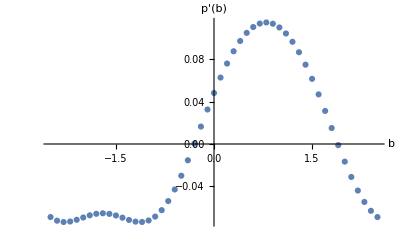

```mathematica
Data1=Range[Length[Data]];
For[i=1,i≤Length[Data],i=i+1,Data1[[i]]={Data[[i]][[1]],Data[[i]][[2]][[1]]}]
p1=ListPlot[Data1,AxesLabel->{"b","p'(b)"}]
```

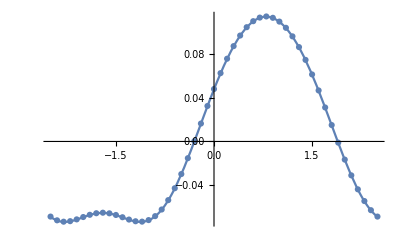

```mathematica
p2=Plot[(-ρ[x]+pprimea+0.387)*L/(2*Pi),{x,a,a+L},PlotRange->All];(*0.387 is actually ρ[a]. For some reason the code kept returning 0 even though the plot above suggests otherwise. The scaling is the ratio between teh coeff of x and coeff of λ in V(x,λ). That is what is needed to make it a function of V(x-λ)*)
Show[p2,p1]
```

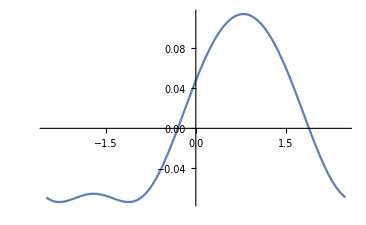

```mathematica
p2
```

Clearly p’(λ) is dependent on b.

```mathematica
(*NIntegrate[ρ1[x]*x,{x,a,a+L}]*)
```

```mathematica
(*Testing out the algorithm*)
```

```mathematica
i := 1
```

```mathematica
k=((2*i-Ntot-1)/(2*Ntot))*2*Pi/L;
```

```mathematica
vals=NDEigenvalues[{-Laplacian[u[x],{x}]-2*I*k*D[u[x],x]+k^2*u[x]+V[x,λ]*u[x],u[a]==u[a+L]},u[x],{x,a,a+L},6]
```

{2.82695+2.03511×10^-14 ⅈ,3.80402-2.93486×10^-14 ⅈ,6.51955-7.61277×10^-15 ⅈ,6.66898-8.82567×10^-15 ⅈ,12.7614-7.56476×10^-15 ⅈ,13.0214-3.88485×10^-15 ⅈ}

```mathematica
n := 1
```

```mathematica
utemp=NDSolve[{-Laplacian[u[x],{x}]-2*I*k*D[u[x],x]+k^2*u[x]+V[x,λ]*u[x]==Re[vals[[n]]]*u[x],u[a]==u[a+L],u[a+0.3*L]==0.23327569085619906},u[x],{x,a,a+L}]
```

{{u[x]→InterpolatingFunction[…][x]}}

```mathematica
Norma=Sqrt[NIntegrate[Abs[Evaluate[u[x]/.utemp]]^2,{x,a,a+L}]]
```

{0.399399}

```mathematica
v[x_]:=Evaluate[u[x]/.utemp]/Norma
```

```mathematica
myperiodic[func_, {val_Symbol, min_?NumericQ, max_?NumericQ}] := func /. (val :> Mod[val - min, max - min] + min)(*periodically extend any function*)
```

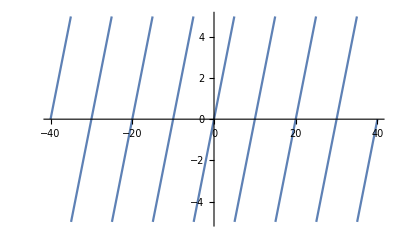

```mathematica
Plot[myperiodic[t, {t, -5, 5}] // Evaluate, {t, -40, 40}](*Testing out my periodic*)
```

```mathematica
g[x_] := myperiodic[v[x], {x, a, a + L}](*periodicaly extending the function*)
```

```mathematica
NIntegrate[Abs[g[x]]^2,{x,a,a+L}]
```

{1.}

```mathematica
Plot[{Re[u[x]], Im[u[x]]}, {x, a, a + L}]
```

-Graphics-

```mathematica
(*Plot[{Re[g[x]],Im[g[x]]}, {x, a, a+L}]*)(*Doesn't seem to work*)
```

```mathematica
NIntegrate[Abs[g[x]]^2*(x-a),{x,a,a+L}]
```

{1.56267}